## Модели прогнозирования

### Литература

1. Holt, C. E. Forecasting seasonals and trends by exponentially weighted averages (1957)
2. Winters, P.R. Forecasting sales by exponentially weighted moving averages (1960)

## 1. Простейшие модели прогнозирования

### 1.1. Прогноз средним

Наиболее простой способ построить прогноз на h точек вперед – посмотреть, какие значения им предшествовали и в качестве прогноза взять среднее значение по всему имеющемуся временному ряду:

(ŷ)_(T+h)=1/T∑_(t=1)^T y_t.

Такой способ позволяет получить прогноз на сколь угодно длительный период времени и в задачах, где нет явных закономерностей во временном ряду, наивный прогноз средним значением является не худшим вариантом. Рассмотрим данные по продажам вина в Австралии. Построим по имеющимся данным прогноз на 12 месяцев вперед:

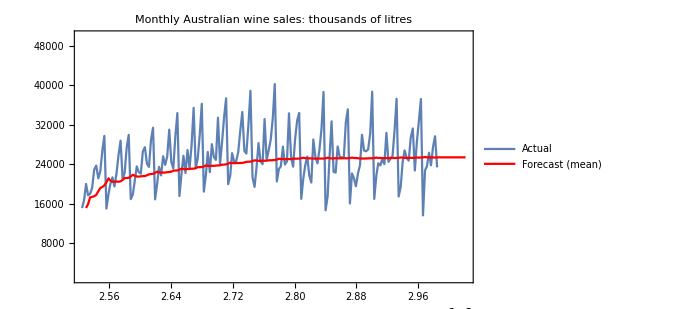

```mathematica
wine=Import["C:\\Users\\akselle\\YandexDisk\\Учебные курсы СПбГЭУ\\ПМ-1601\\monthly-australian-wine-sales-th.csv"];
foldMean=(Mean/@FoldList[Join,{},List/@wine⟦2;;-4,2⟧])⟦2;;⟧;
mean1=ConstantArray[Mean[wine⟦2;;-4,2⟧],12];
dates2=With[{first=DateObject[wine⟦3,1⟧]},DateRange[first,DatePlus[first, Quantity[188,"Months"]],{1, "Month"}]];
forecastMean1=TemporalData[Thread[{dates2⟦2;;⟧,Join[foldMean,mean1]}]];
DateListPlot[{{DateObject[#⟦1⟧],#⟦2⟧}&/@wine⟦2;;-4⟧,forecastMean1},Joined->True,PlotLegends->{"Actual","Forecast (mean)"},ImageSize->500,PlotStyle->{Automatic,Red},PlotRange->{All,{1000,50000}},PlotLabel->"Monthly Australian wine sales: thousands of litres"]
```

Очевидны недостатки такого способа прогнозирования. Если в данных наблюдается тренд, то среднее значение плохо описывает динамику поведения ряда. Это хорошо видно на примере задачи прогнозирования объемов пассажирских авиаперевозок.

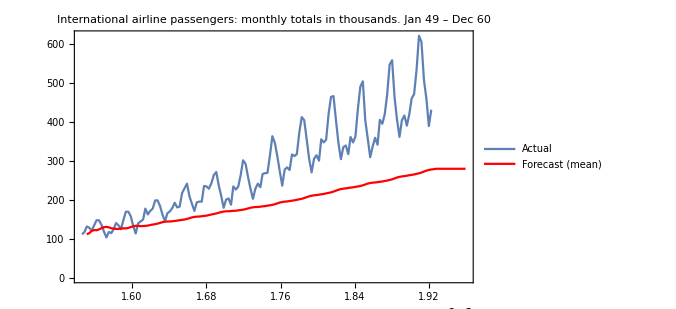

```mathematica
passengers=ExampleData[{"Statistics","InternationalAirlinePassengers"},"TimeSeries"];
foldMean=(Mean/@FoldList[Join,{},List/@Normal[passengers]⟦All,2⟧])⟦2;;⟧;mean1=ConstantArray[Mean[Normal[passengers]⟦All,2⟧],12];
dates=With[{first=Normal[passengers]⟦2,1⟧},DateRange[first,DatePlus[first, Quantity[(Normal[passengers]⟦All,2⟧//Length)+12,"Months"]],{1, "Month"}]];
forecastMean1=TemporalData[Thread[{dates⟦2;;⟧,Join[foldMean,mean1]}]];
DateListPlot[{passengers,forecastMean1},Joined->True,PlotLegends->{"Actual","Forecast (mean)"},PlotStyle->{Automatic,Red},ImageSize->500,PlotLabel->"International airline passengers: monthly totals in thousands. Jan 49 – Dec 60"]
```

Как видно на графике, прогноз начинает сильно отставать от тренда из-за того, что значения признака в начале ряда довольно маленькие по сравнению со значениями в конце ряда и «перетягивают» на себя прогноз.

### 1.2. Скользящее среднее

Чтобы сгладить недостатки предыдущего метода прибегают к методу скользящего среднего. В данном методе прогноз будущего значения признака зависит от среднего от k последних наблюдений:

(ŷ)_(T+h)=1/k∑_(t=T-k)^T y_t.

Долгосрочный прогноз таким способом построить не удастся, поскольку каждое следующее значение зависит от фактически наблюдаемых величин. Однако скользящее среднее позволяет сгладить исходный ряд, выявив таким образом тренд и предоставляя возможность обнаружить закономерности в данных.

Построим модель скользящего среднего на примере продаж вина в Австралии, чтобы убедиться в отсутствии в нем тренда.

```mathematica
DynamicModule[{data=wine⟦2;;-4⟧,dlplt,maplt,dates,forecastMA,movingAvg},
Manipulate[movingAvg=MovingAverage[data⟦All,2⟧,k];
dates=With[{first=DateObject[data⟦k+1,1⟧]},DateRange[first,DatePlus[first, Quantity[Length[movingAvg],"Months"]],{1, "Month"}]];
forecastMA=TemporalData[Thread[{dates⟦2;;⟧,movingAvg}]];
dlplt=DateListPlot[{DateObject[#⟦1⟧],#⟦2⟧}&/@data,Joined->True,ImageSize->500,PlotRange->{All,{1000,50000}},PlotLabel->"Monthly Australian wine sales: thousands of litres"];
maplt=DateListPlot[forecastMA,Joined->True,ImageSize->500,PlotRange->{All,{1000,50000}},PlotStyle->Red];
If[k==1,dlplt,Show[{dlplt,maplt}]],
{k,1,12,1}
]
]
```

Напротив, на примере данных об объемах пассажирских авиаперевозок при применении метода скользящего среднего четко виден повышающийся тренд. Кроме того, при применении метода меньших порядков становятся более очевидными сезонные колебания.

```mathematica
DynamicModule[{data=Normal[passengers],dlplt,maplt,dates,forecastMA,movingAvg},
Manipulate[movingAvg=MovingAverage[data⟦All,2⟧,k];
dates=With[{first=data⟦k+1,1⟧},DateRange[first,DatePlus[first, Quantity[Length[movingAvg],"Months"]],{1, "Month"}]];
forecastMA=TemporalData[Thread[{dates⟦2;;⟧,movingAvg}]];
dlplt=DateListPlot[{DateObject[#⟦1⟧],#⟦2⟧}&/@data,Joined->True,ImageSize->500,PlotLabel->"International airline passengers: monthly totals in thousands. Jan 49 – Dec 60"];
maplt=DateListPlot[forecastMA,Joined->True,ImageSize->500,PlotStyle->Red];
If[k==1,dlplt,Show[{dlplt,maplt}]],
{k,1,12,1}
]
]
```

### 1.2. Наивный прогноз

Еще более простой метод краткосрочного прогнозирования основан на предположении, что будущие значения переменной зависят от последнего наблюдаемого значения:

(ŷ)_(T+h)=y_T.

Преимущество такого подхода в простоте реализации, а также отсутствии необходимости в большом количестве исторических данных. Однако очевидным серьезным недостатком такого подхода является низкое качество результатов прогнозирования. Если развивать эту идею, то в качестве прогноза можно брать предыдущие значения с сезонным лагом, если в данных наблюдается сезонность:

(ŷ)_(T+h)=y_(T+h-kS), k=⌊(h-1)/S⌋+1,

где S – период сезонности, ⌊_⌋ – частное от деления.

### 1.3. Экстраполяция тренда

При наличии во временном ряду тренда, можно усложнить наивную модель с помощью экстраполяции тренда:

(ŷ)_(T+h)=y_T+h (y_T-y_1)/(T-1).

Второе слагаемое в данной модели представляет собой ничто иное как уравнение прямой, проходящей через две заданные точки, а именно через первую и последнюю точки временного ряда. Таким образом можно построить долгосрочный прогноз, однако представленная модель не учитывает сезонные колебания.

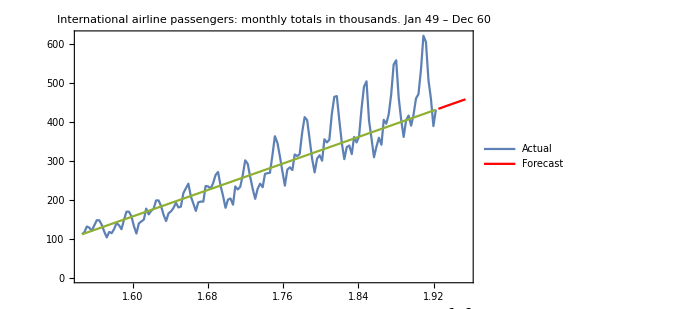

```mathematica
trend=(Normal[passengers]⟦-1,2⟧-Normal[passengers]⟦1,2⟧)/(Length[Normal@passengers]-1)*#&/@Range[12];
forecastTrend=Normal[passengers]⟦-1,2⟧+trend;
dates=With[{last=Normal[passengers]⟦-1,1⟧},DateRange[last,DatePlus[last, Quantity[12,"Months"]],{1, "Month"}]];
forecastTrend1=TemporalData[Thread[{dates⟦2;;⟧,forecastTrend}]];
DateListPlot[{passengers,forecastTrend1,{{Normal[passengers]⟦1,1⟧,Normal[passengers]⟦1,2⟧},{Normal[passengers]⟦-1,1⟧,Normal[passengers]⟦-1,2⟧}}},Joined->True,PlotLegends->{"Actual","Forecast"},PlotStyle->{Automatic,Red},ImageSize->500,PlotLabel->"International airline passengers: monthly totals in thousands. Jan 49 – Dec 60"]
```

## 2. Адаптивные методы прогнозирования

### 2.1. Простое экспоненциальное сглаживание

Экспоненциальное сглаживание использует идею метода скользящего среднего с той лишь разницей, что каждое предшествующее наблюдение имеет свой вес, экспоненциально убывающий по мере углубления в историю:

(ŷ)_(T+1|T)=α y_T+α(1-α)y_(T-1)+(α(1-α))^2 y_(T-2)+…,

где α∈[0;1].

Чем больше параметр сглаживания α, тем больший вес имеют последние наблюдения.

```mathematica
Grid[{
{"Наблюдение","α=0.2","α=0.4","α=0.6","α=0.8"},
{"y","0.2","0.4","0.6","0.8"},
{"y",0.2(1-0.2),0.4(1-0.4),0.6(1-0.6),0.8(1-0.8)},
{"y",0.2(1-0.2)^2,0.4(1-0.4)^2,0.6(1-0.6)^2,0.8(1-0.8)^2},
{"y",0.2(1-0.2)^3,0.4(1-0.4)^3,0.6(1-0.6)^3,0.8(1-0.8)^3},
{"y",0.2(1-0.2)^4,0.4(1-0.4)^4,0.6(1-0.6)^4,0.8(1-0.8)^4},
{"y",0.2(1-0.2)^5,0.4(1-0.4)^5,0.6(1-0.6)^5,0.8(1-0.8)^5},
{"y",0.2(1-0.2)^6,0.4(1-0.4)^6,0.6(1-0.6)^6,0.8(1-0.8)^6}
},Frame->All,ItemStyle->{FontFamily->"Georgia",14}]
```

Наблюдение | α=0.2 | α=0.4 | α=0.6 | α=0.8
y | 0.2 | 0.4 | 0.6 | 0.8
y | 0.16 | 0.24 | 0.24 | 0.16
y | 0.128 | 0.144 | 0.096 | 0.032
y | 0.1024 | 0.0864 | 0.0384 | 0.0064
y | 0.08192 | 0.05184 | 0.01536 | 0.00128
y | 0.065536 | 0.031104 | 0.006144 | 0.000256
y | 0.0524288 | 0.0186624 | 0.0024576 | 0.0000512

Модель экспоненциального сглаживания можно выразить через рекуррентную формулу. В частности, метод Брауна можно сформулировать следующим образом:

(ŷ)_(t+1|t)=l_t,
l_t=α y_t+(1-α)l_(t-1),

где l_t – ожидаемое значение ряда или уровень. Таким образом, прогноз на один шаг вперед можно записать в виде:

(ŷ)_(T+1|T)=∑_(i=0)^(T-1) (α(1-α))^i y_(T-i)+(1-α)^T l_0.

Данный метод подход для краткосрочного прогнозирования рядов без тренда и сезонности.

```mathematica
passengers=Normal[ExampleData[{"Statistics","InternationalAirlinePassengers"},"TimeSeries"]];
alpha = 0.5;
data=passengers[[All,2]];
```

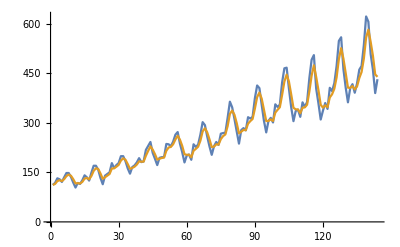

```mathematica
Subscript[y, 1]=data[[1]];
newdata=Table[Subscript[y, t+1]=alpha*data[[t]]+(1-alpha)*Subscript[y, t],{t,1,Length@data}];
ListLinePlot[{data,newdata}]
```

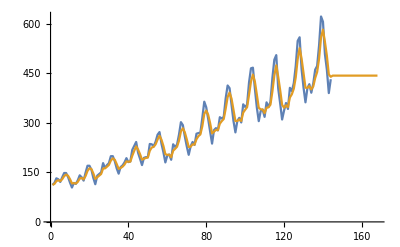

```mathematica
e=Length@newdata;
Do[Subscript[y, e+1]=alpha*newdata[[e]]+(1-alpha)*Subscript[y, e];newdata=Append[newdata,Subscript[y, e+1]];e=e+1,24]
ListLinePlot[{data,newdata}]
```

### 2.2. Метод Хольта

Учесть тренд позволяет метод Хольта, который предполагает разбиение временного ряда на две составляющие: уровень l_t и тренд b_t. По сравнению с методом Брауна экспоненциальное сглаживание применяется также к тренду в предположении, что будущее направление изменения ряда зависит от взвешенных предыдущих изменений. В случае линейного тренда:

(ŷ)_(t+1|t)=l_t,
l_t=α y_t+(1-α)l_(t-1),

(ŷ)_(t+h|t)=l_t+h b_t,
l_t=α y_t+(1-α)(l_(t-1)+b_(t-1)),
b_t=β(l_t-l_(t-1))+(1-β)b_(t-1),

где α,β∈[0;1]. Теперь компонента, описывающая уровень, зависит от текущего значения ряда, а второе слагаемое разбивается на предыдущее значения уровня и тренда. В свою очередь компонента, отвечающая за тренд, зависит от изменения уровня на текущем шаге, и от предыдущего значения тренда. Результирующее значение прогноза представляет собой сумму модельных значений уровня и тренда.

```mathematica
passengers=Normal[ExampleData[{"Statistics","InternationalAirlinePassengers"},"TimeSeries"]];
alpha = 0.5;
beta=0.25;
data=passengers[[All,2]];
```

1

{113.375,117.141,127.881,131.891,128.535,134.665,145.896,151.775,146.743,132.259,113.984,112.349,110.363,116.824,130.577,135.006,130.97,143.206,163.173,174.01,171.427,152.832,129.181,131.708,137.132,143.953,165.62,168.625,175.05,181.631,197.593,205.749,199.609,180.838,159.097,159.09,163.075,171.683,185.152,185.367,186.179,208.063,227.746,245.37,233.136,212.752,187.965,187.327,189.092,190.838,217.356,232.32,236.388,246.248,263.897,277.734,262.061,234.842,198.877,191.66,191.094,182.424,208.161,219.385,230.323,255.002,292.216,306.421,290.596,259.984,224.555,220.396,227.517,227.263,249.103,263.51,272.025,304.154,352.2,367.072,350.125,313.135,266.624,265.29,269.962,269.677,295.451,308.531,318.755,358.772,405.059,424.196,400.114,351.809,300.056,292.422,295.927,291.314,324.593,340.159,353.296,401.953,455.663,484.934,457.954,402.094,341.027,325.366,321.364,307.943,329.989,336.264,350.243,403.827,469.516,513.796,471.711,414.08,347.755,326.747,331.9,326.739,366.066,384.472,410.115,456.673,529.367,574.919,535.705,472.009,403.911,391.497,394.479,382.534,395.121,430.649,459.081,514.288,598.855,634.032,586.866,524.05,440.386,418.505}

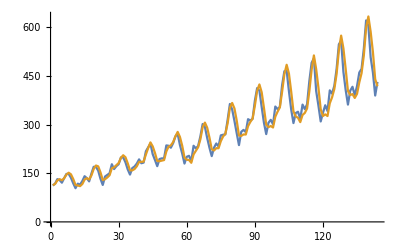

```mathematica
Subscript[l, 1]=data[[1]];
Subscript[te, 1]=1;
newdata={};
e=1;
h=1
Do[Subscript[l, e+1]=alpha*data[[e]]+(1-alpha)*(Subscript[l, e]+Subscript[te, e]);Subscript[te, e+1]=beta*(Subscript[l, e+1]-Subscript[l, e])+(1-beta)*Subscript[te, e];Subscript[y, e+h]=Subscript[l, e+1]+h*Subscript[te, e+1];newdata= Append[newdata,Subscript[y, e+h]];e++,Length@data];
newdata
ListLinePlot[{data,newdata}]
```

{113.375,117.141,127.881,131.891,128.535,134.665,145.896,151.775,146.743,132.259,113.984,112.349,110.363,116.824,130.577,135.006,130.97,143.206,163.173,174.01,171.427,152.832,129.181,131.708,137.132,143.953,165.62,168.625,175.05,181.631,197.593,205.749,199.609,180.838,159.097,159.09,163.075,171.683,185.152,185.367,186.179,208.063,227.746,245.37,233.136,212.752,187.965,187.327,189.092,190.838,217.356,232.32,236.388,246.248,263.897,277.734,262.061,234.842,198.877,191.66,191.094,182.424,208.161,219.385,230.323,255.002,292.216,306.421,290.596,259.984,224.555,220.396,227.517,227.263,249.103,263.51,272.025,304.154,352.2,367.072,350.125,313.135,266.624,265.29,269.962,269.677,295.451,308.531,318.755,358.772,405.059,424.196,400.114,351.809,300.056,292.422,295.927,291.314,324.593,340.159,353.296,401.953,455.663,484.934,457.954,402.094,341.027,325.366,321.364,307.943,329.989,336.264,350.243,403.827,469.516,513.796,471.711,414.08,347.755,326.747,331.9,326.739,366.066,384.472,410.115,456.673,529.367,574.919,535.705,472.009,403.911,391.497,394.479,382.534,395.121,430.649,459.081,514.288,598.855,634.032,586.866,524.05,440.386,418.505,410.071,390.697,371.323,351.948,332.574,313.2,293.825,274.451,255.077,235.702,216.328,196.954,177.579,158.205,138.831}

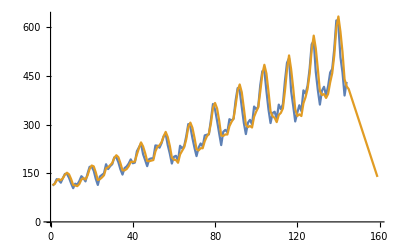

```mathematica
e=Length@newdata;
Do[Subscript[l, e+1]=alpha*newdata[[e]]+(1-alpha)*(Subscript[l, e]+Subscript[te, e]);Subscript[te, e+1]=beta*(Subscript[l, e+1]-Subscript[l, e])+(1-beta)*Subscript[te, e];Subscript[y, e+h]=Subscript[l, e+1]+h*Subscript[te, e+1];newdata= Append[newdata,Subscript[y, e+h]];e++,10];
newdata
ListLinePlot[{data,newdata}]
```

### 2.3. Метод Хольта-Уинтерса

Модель Хольта-Уинтерса является модификацией модели Хольта. Данная модификация позволяет учесть не только последние наблюдаемые значения и тренд, но и сезонность. Дополнительная сезонная компонента в модели объясняет повторяющиеся колебания вокруг уровня и тренда и характеризуется длиной сезона m:

(ŷ)_(t+h|t)=l_t+h b_t+s_(t-m+(h mod m)),
l_t=α(y_t-s_(t-m))+(1-α)(l_(t-1)+b_(t-1)),
b_t=β(l_t-l_(t-1))+(1-β)b_(t-1),
s_t=γ(y_t-l_(t-1)-b_(t-1))+(1-γ)s_(t-m).

Уровень теперь зависит от текущего значения ряда без учета соответствующей сезонной компоненты, а сезонная компонента зависит от текущего значения ряда за вычетом уровня и от предыдущего значения компоненты.